```mathematica
Clear["Subscript"]
```

```mathematica
M=1;
```

```mathematica
a=0.2;
```

```mathematica
f[r_]:=1-(2M r^2)/((a^2+r^2)^(3/2))
```

```mathematica
g[x_]:=1-(2M x)/((a^2 x^2+1)^(3/2))
```

SetDelayed::write: 0.1[x_] 中的标签 Real 被保护.

$Failed

```mathematica
event=NSolveValues[f[r]==0,r]
```

{-1.96946,1.96946,0.0687757,-0.0687757}

```mathematica
ev=event[[2]]
```

1.96946

```mathematica
sol=N@SolveValues[r^2-bc^2 f[r]==0&&2 bc^2 f[r]^2-r^3 D[f[r],r]==0&&2<=r<=3&&5<=bc<=6,{bc,r},Reals]
```

SolveValues::ratnz: SolveValues 无法求解具有不精确系数的系统. 答案是通过求解相应的精确系统并且将结果数值化处理得到的.

{{5.16108,2.96617}}

```mathematica
ss=sol[[1,1]]
```

5.16108

```mathematica
sss=sol[[1,2]]
```

2.96617

```mathematica
g[u_]:=1-(2M u)/((1+(a u)^2)^(3/2));
```

SetDelayed::write: 0.1[u_] 中的标签 Real 被保护.

```mathematica
Function[u,g[u]]
```

Function[u,g[u]]

```mathematica
turn[b_?NumericQ]:=Block[{sol},sol=Quiet@NSolve[{1/b^2-y^2 g[y]==0,6>y>0},y,Reals];
If[sol==={},$Failed,y/. First@sol]]
```

```mathematica
ϕ[b_]:=Chop[NIntegrate[1/Sqrt[1/b^2-x^2  g[x]],{x,0,turn[b]}],10^-6]
```

```mathematica
ψ[b_]:=NIntegrate[1/Sqrt[1/b^2-x^2 g[x]],{x,0,1/ev}]
```

NIntegrate::inumr: 在以 {{0,0.50189}} 为界的区域内，对于所有采样点，计算被积函数 1/(√(689534.-x^2 0.1[x])) 得到非数值.

NIntegrate::inumr: 在以 {{0.,0.50189}} 为界的区域内，对于所有采样点，计算被积函数 1./(√(689534.-1. x^2 0.1[x])) 得到非数值.

General::stop: 在本次计算中，NIntegrate::inumr 的进一步输出将被抑制.

ReplaceAll::reps: {0.0355087-y^2 0.1[y]==0,6>y>0} 既不是替换规则列表，也不是一个有效的分派表，因此无法用来替换.

ReplaceAll::reps: {0.0355087-1. y^2 0.1[y]==0.,6.>y>0.} 既不是替换规则列表，也不是一个有效的分派表，因此无法用来替换.

General::stop: 在本次计算中，ReplaceAll::reps 的进一步输出将被抑制.

NIntegrate::nlim: x = y/.{0.0355087-1. y^2 0.1[y]==0.,6.>y>0.} 不是积分的一个有效的极限.

General::stop: 在本次计算中，NIntegrate::nlim 的进一步输出将被抑制.

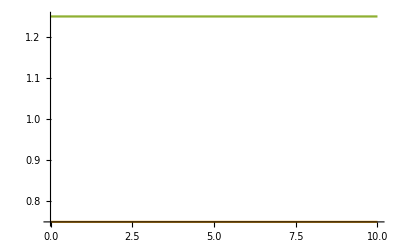

```mathematica
Plot[{Piecewise[{{{ψ[b]/(Pi 2)},0.001<b<ss},{{ϕ[b]/Pi},b>=ss}}],3/4,5/4},{b,0.001,10}]
```